```mathematica
SetDirectory[NotebookDirectory[]];
```

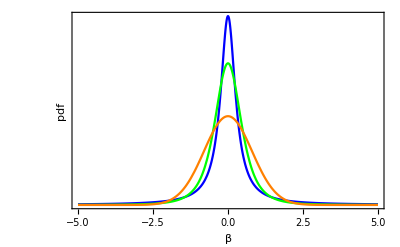

```mathematica
gFinal=Plot[{PDF[CauchyDistribution[0,0.3],x],PDF[StudentTDistribution[0,Sqrt[(0.64(-2+3))/3],3],x],PDF[NormalDistribution[0,0.8],x]},{x,-5,5},PlotRange->Full,PlotStyle->{Blue,Green,Orange},Frame->{True,True,False,False},AxesOrigin->{-5,0},FrameTicks->{True,None},BaseStyle->Medium,FrameLabel->{"β","pdf"}]
```

```mathematica
Export["Distributions_cauchyPrior.pdf",gFinal]
```

Distributions_cauchyPrior.pdf

```mathematica
PDF[CauchyDistribution[0,a],x]
```

1/(a π (1+x^2/a^2))

```mathematica
PDF[StudentTDistribution[0,a,1],x]
```

1/(a π (1+x^2/a^2))

```mathematica
Solve[Simplify[Variance@StudentTDistribution[0,Sqrt@sigma,ν],ν>2]==var,{sigma}][[1,1,2]]
```

(var (-2+ν))/ν

```mathematica
Variance@StudentTDistribution[0,Sqrt[(0.64(-2+7))/7],7]
```

0.64

```mathematica
Variance@NormalDistribution[0,0.8]
```

0.64